```mathematica
Needs["PacletManager`"]
PacletInstall["Wolfram Mathematica/IGraphM-0.6.5.paclet"]
(*G=Import["~/Downloads/r44_16.g6"];*)
(*Length[G]*)
```

System`PacletInstall::samevers: A paclet named IGraphM with the same version number (0.6.5) is already installed. Use PacletUninstall to remove the existing version first, or call PacletInstall with ForceVersionInstall -> True.

$Failed

```mathematica
PacletObject[…]
```

PacletObject[…]

Needs::cxt: Invalid context specified at position 1 in Needs[IGraphM]. A context must consist of valid symbol names separated by and ending with `.

```mathematica
Needs["IGraphM`"]
```

IGraph/M 0.6.5 (December 21, 2022)
Evaluate IGDocumentation[] to get started.

```mathematica
{{"IGraph/M 0.6.5 (December 21, 2022)"}, {"Evaluate \!\(\*ButtonBox[\"IGDocumentation[]\",BaseStyle->\"Link\",ButtonData->\"paclet:IGraphM\"]\) to get started."}}
IGVersion[]
```

IGraph/M 0.6.5 (December 21, 2022)
Evaluate IGDocumentation[] to get started.

IGraph/M 0.6.5 (December 21, 2022)
igraph 0.9.10-23-g5635203bd (Dec 21 2022)
Microsoft Windows (64-bit)

```mathematica
"IGraph/M 0.6.5 (December 21, 2022)\nigraph 0.9.10-23-g5635203bd (Dec 21 2022)\nMicrosoft Windows (64-bit)";
G = Import["Grafencollectie\\r55_42some.g6"];
Length[G]
```

328

```mathematica
imax=100;
T=Table[0,imax];
L1=T;L2=T; L3 = T; C1=T;
E1={};E2={};
For[i=1,i<=imax,i++,
eigs1=Sort[N[Eigenvalues[AdjacencyMatrix[G[[i]]]]]];
L1[[i]]=eigs1[[-1]];
R=IGRewire[G[[i]],10000];
eigs2=Sort[N[Eigenvalues[AdjacencyMatrix[R]]]];
L2[[i]]=eigs2[[-1]];
R2 = RandomGraph[BernoulliGraphDistribution[22, 0.5]];
eigs3 = Sort[N[Eigenvalues[AdjacencyMatrix[R2]]]];
L3[[i]] = eigs3[[-1]];
E1=Join[E1,eigs1[[1;;-2]]];
E2=Join[E2,eigs2[[1;;-2]]];
C1[[i]]=Length[Select[Mod[eigs1,1],LessThan[0.0001]]];
]
Show[{Plot[42/5-1, {t, 0, 100}, PlotStyle -> Dashed, PlotLabels-> "n/α-1"],ListPlot[L1,PlotStyle->Red],ListPlot[L2, PlotStyle -> Green]},PlotRange->{{0, 120}, {0, 21}}]
```

-Graphics-

```mathematica
Show[%171,AxesLabel->{None,HoldForm[Subscript[λ, max]]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

-Graphics-

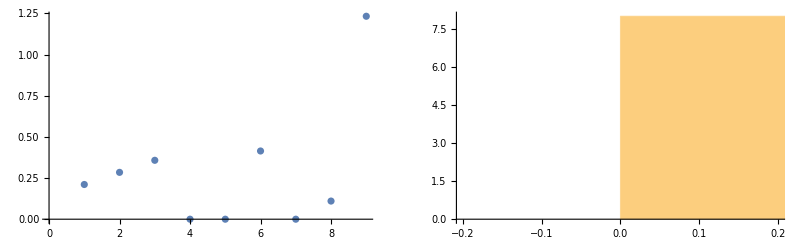

```mathematica
(*Difference between the second-largest eigenvalues in the graphs and the null model*)GraphicsRow[{ListPlot[(L2-L1)/L1],Histogram[(L2-L1)/L1,PlotRange->{{-0.2,0.2},All}]}]
```

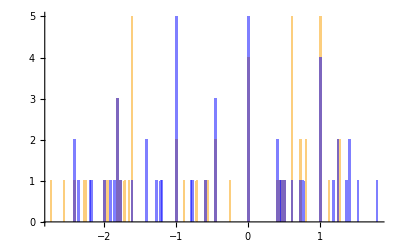

```mathematica
(*Accumulated specturm over all set, continuous part*)Show[{Histogram[E1,200],Histogram[E2,200,ChartStyle->{Directive[Blue,Opacity[.5]]}]},PlotRange->All]
```

```mathematica
(*Total number of integer eigenvalues:*)
Total[C1]
```

61

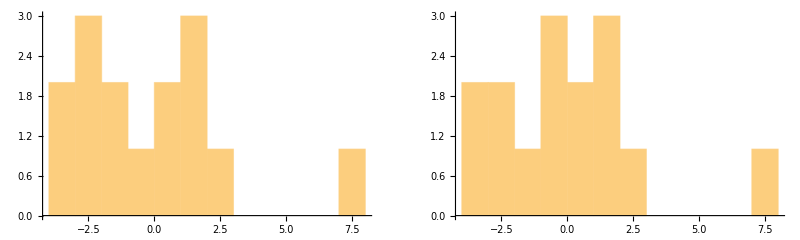

(-3.16105 | -3.65216 | -0.491109
-3.16105 | -3.47286 | -0.311808
-2.46407 | -2.80791 | -0.343839
-2.46407 | -2.00324 | 0.460836
-2.39745 | -1.74082 | 0.656632
-1.17432 | -0.834754 | 0.339566
-1.17432 | -0.80846 | 0.36586
-0.24431 | -0.319985 | -0.0756756
0.834644 | 0.60033 | -0.234314
0.834644 | 0.75299 | -0.0816541
1.41808 | 1.29186 | -0.126221
1.9648 | 1.66275 | -0.302046
1.9648 | 1.7143 | -0.2505
2. | 2.39361 | 0.393612
7.22368 | 7.22434 | 0.00066061)

```mathematica
(*Example of spectrum*)
GraphicsRow[{Histogram[eigs1,14],Histogram[eigs2,14]}]
Transpose[{eigs1,eigs2,eigs2-eigs1}]//MatrixForm
```

```mathematica
G = Import["Grafencollectie\\r44_15.g6"];
Len=Min[100, Length[G]];
n=15; K1=3; K2=3;
B = N[Sqrt[(2-1/K1-1/K2)*n*(n-1)]];
T=Table[0, Len];
L1=T; L2=T; L3=T;
For[i=1, i<= Len, i++,
Geig1 = Sort[N[Eigenvalues[AdjacencyMatrix[G[[i]]]]]][[-1]];
G2 = GraphComplement[G[[i]]];
Geig2 = Sort[N[Eigenvalues[AdjacencyMatrix[G[[i]]]]]][[-1]];
L1[[i]]=Geig1+Geig2;
R = RandomGraph[BernoulliGraphDistribution[n, 0.5]];
Reig1 = Sort[N[Eigenvalues[AdjacencyMatrix[R]]]][[-1]];
R2 = GraphComplement[R];
Reig2 = Sort[N[Eigenvalues[AdjacencyMatrix[R2]]]][[-1]];
L2[[i]] = Reig1+Reig2;
S = IGRewire[G[[i]], 10 000];
Seig1 = Sort[N[Eigenvalues[AdjacencyMatrix[S]]]][[-1]];
S2 = GraphComplement[S];
Seig2 = Sort[N[Eigenvalues[AdjacencyMatrix[S2]]]][[-1]];
L3[[i]] = Seig1 + Seig2;
]
Show[{Plot[B, {t, 0, 100}, PlotStyle -> {Blue, Dashed}, PlotLabels->"Ni"],ListPlot[L1, PlotStyle->Red],ListPlot[L3, PlotStyle->Green]}, PlotRange-> All]
```

-Graphics-